1+√(1-a^2)

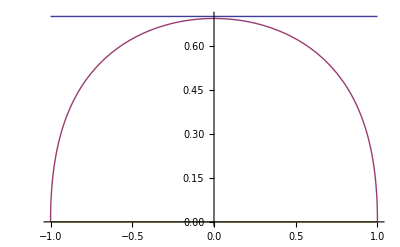

```mathematica
rh=1+Sqrt[1-a^2]
Plot[{0.7,Log[rh],0},{a,-1,1}]
```

```mathematica
Solve[rh==myrh,a]
```

{{a→-√(2 myrh-myrh^2)},{a→√(2 myrh-myrh^2)}}

```mathematica
it1=√(2 myrh-myrh^2)//.{myrh->3-Exp[x1]}
it2=1
```

√(2 (3-ⅇ^x1)-(3-ⅇ^x1)^2)

1

```mathematica
it1=√(2 myrh-myrh^2)//.{myrh->10^(x1)}
it2=√(2 myrh-myrh^2)//.{myrh->1+Sqrt[1-x1^2]}
```

√(2^(1+x1) 5^x1-10^(2 x1))

√(2 (1+√(1-x1^2))-(1+√(1-x1^2))^2)

```mathematica
sx1=Log[2]
NN=8
dx1=-Log[2]/(NN-1)
x1=sx1+i*dx1
mysols=Solve[x1==Log[1+Sqrt[1-a^2]],a]
it1=mysols[[2,1,2]]
```

Log[2]

8

-Log[2]/7

Log[2]-1/7 i Log[2]

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{a→-2 √(-2^(-2 i/7)+2^(-i/7))},{a→2 √(-2^(-2 i/7)+2^(-i/7))}}

2 √(-2^(-2 i/7)+2^(-i/7))

```mathematica
it1//.{i->0}
```

0

```mathematica
it2=0+i/(NN-1)
```

i/7

```mathematica
dit1=D[it1,i];
dit2=D[it2,i];
```

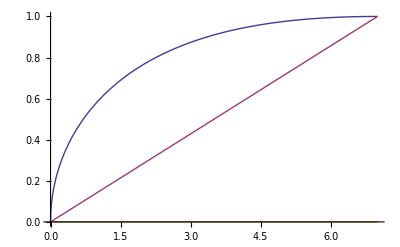

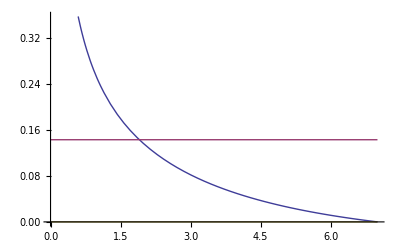

```mathematica
Plot[{it1,it2,0},{i,0,NN-1}]
Plot[{dit1,dit2,0},{i,0,NN-1}]
```